# Plot the G-function G(v,u,x,m) over focal strategy v

Here, we plot the G-function G(v,u,x,m) over the focal player strategy v for given dominant strategy u, population size x and leader strategy m. We implement and plot the G-function defined by eqn. (5.1) in the paper. We want to encourage the reader to implement its own G-function and play around with the code.

### Define the G-function

```mathematica
carry[v_]:=Kmax*Exp[-v^2/sigmaK^2]
H[v_,m_]:=m*Exp[-v^2/sigmaH^2]
G[v_,u_,x_,m_]:=r*( 1-(x/carry[v]))-H[v,m]
```

### Set the parameters of the model

```mathematica
sigmaH=1
sigmaK=1
Kmax=10000
r=1
```

### Plot G(v,u,x,m) over v for given u, x and m

```mathematica
Manipulate[Plot[G[v,u,x,m],{v,-1.0,1.0}],{u,0,10},{x,1,10000},{m,0,1},Frame->True,FrameLabel->{"Focal strategy (v)","G(v,u,x,m)"},LabelStyle->"Subtitle"]
```

## Plot G(v,u,x,m) at the eco-evolutionary equilibrium

In the paper, we plot G at the eco-evolutionary equilibrium. Here, we briefly describe an example how to make this plot.

### Set the parameters (all execpt x and u)

```mathematica
sigmaH=0.5
sigmaK=0.5
r=1.0
m=0.75
Kmax=10000
```

0.5

0.5

1.

0.75

10000

### Compute the eco-evolutionary equilibrium for the given parameter values

We choose u*+ from the paper as an example. More details are in file “ESS.nb” and the supplementary.

```mathematica
ustar1= sigmaH √Log[(m sigmaH^2+m sigmaK^2)/(r sigmaH^2)]
```

0.318381

We then calculate the ecological equilibrium corresponding to this evolutionary equilibrium.

```mathematica
xstar[u_,m_]:=(ⅇ^(-u^2/sigmaH^2-u^2/sigmaK^2) Kmax (-m+ⅇ^(u^2/sigmaH^2) r))/r
```

```mathematica
xstar1=xstar[ustar1,m]
```

3333.33

Eventually, we plot G at this given ustar and xstar and m.

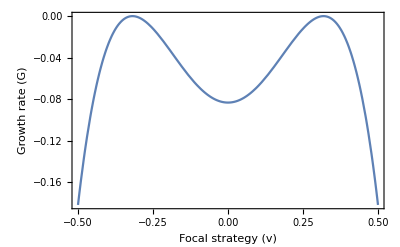

```mathematica
Plot[G[v,ustar1,xstar1,m],{v,-0.5,+0.5},Frame->True,FrameLabel->{"Focal strategy (v)","Growth rate (G)"},LabelStyle->"Subtitle"]
```